```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc

## MMC

```mathematica
{TogglerBar[Dynamic[cfiles],FileNames["*.confs"],Appearance->"Vertical"],TogglerBar[Dynamic[efiles],FileNames["*.en"],Appearance->"Vertical"],TogglerBar[Dynamic[hfiles],FileNames["*.hist"],Appearance->"Vertical"]}
```

{






,






,


}

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"List"]&/@efiles;

data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

{{100,100},{2500,2500}}

{11,1001}

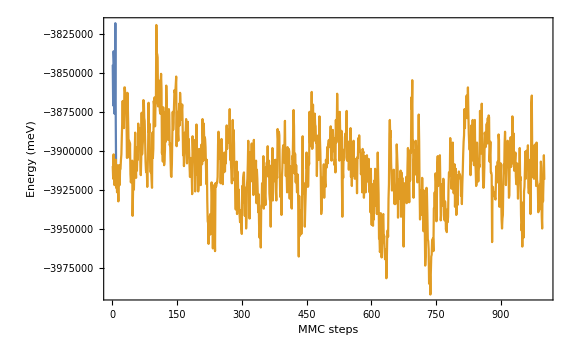

```mathematica
ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large]
```

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
```

```mathematica
(size[[1]] hist[[1,-1]])/nhsteps[[-1]]
```

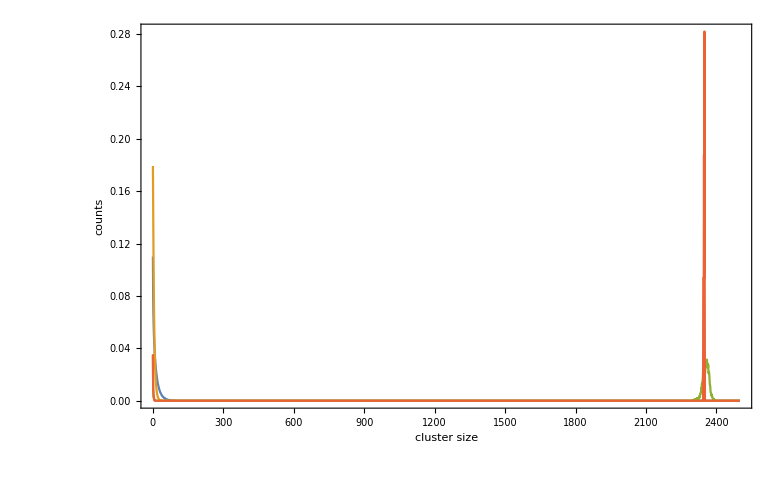

```mathematica
ListLinePlot[{(size hist[[-1]])/(nhsteps[[-1]]nads2),(size hist3[[-1]])/(nhsteps3[[-1]]nads3),(size hist5[[-1]])/(nhsteps5[[-1]]nads5),(size hist5[[1]])/(nhsteps5[[1]]nads5)},FrameLabel->{"cluster size","counts"},PlotRange->{All,All}]
```

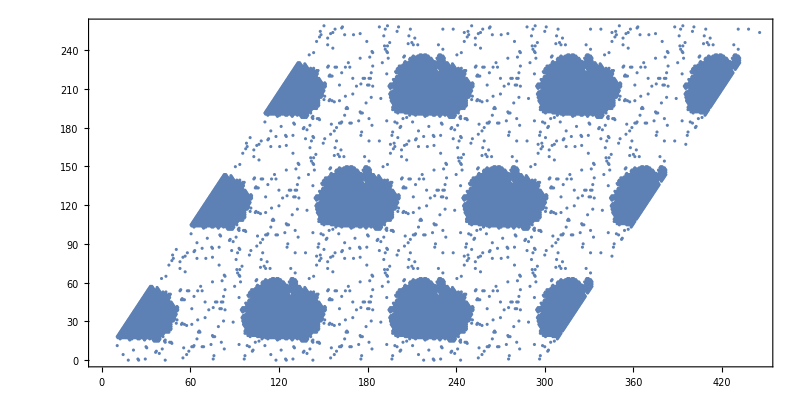

```mathematica
ListPlot[(((#-{1,1})&/@Position[ArrayPad[occs5[[-1]],nlat,"Periodic"],1]).{{1,0},{Cos[π/3],Sin[π/3]}}),AspectRatio->Cos[π/3]]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs5[[i]],nlat,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```

Part::partd: Part specification occs5⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument occs5⟦1⟧ to ArrayPad should be an array.

MatrixPlot::mat0: Argument occs5⟦1⟧ at position 1 is not a matrix.

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs3[[i]],0,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```

## KMC

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data

```mathematica
FileNames["*.pos"]
```

{kmc000001.pos,kmc000002.pos,kmc000003.pos,kmc000004.pos,kmc000005.pos,kmc000006.pos,kmc000007.pos,kmc000008.pos,kmc000009.pos,kmc000010.pos}

```mathematica
data=Import[#,"Table"]&/@FileNames["*.pos"];
time=data[[All,All,1]];
i=data[[All,All,2]];
j=data[[All,All,3]];
```

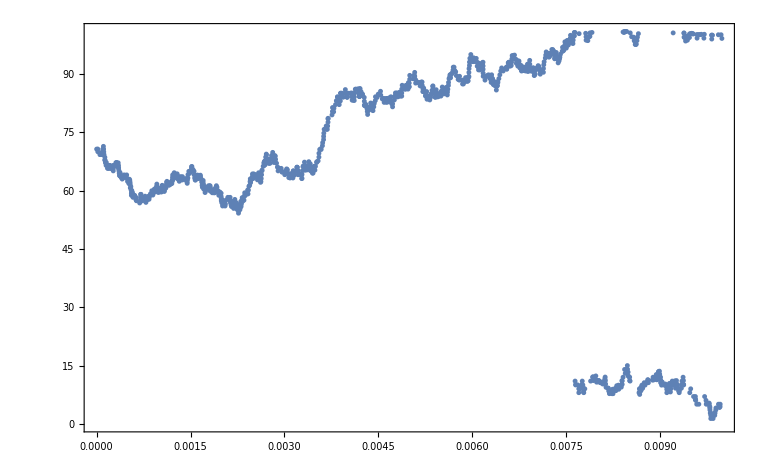

```mathematica
ListPlot[{time[[1]],√(i[[1]]^2+j[[1]]^2)}ᵀ]
```